## Fixed M_Z'=10 TeV, Fixed Brane parameter = 0.8, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL08=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.8)
```

0.799871

```mathematica
Zprime10decayfixedmass08[CvR_]:=MassZprime10/(12π)(1/4(CvL08+CvR)^2+1/4(CvL08-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL08+CvR)^2-1/2(CvL08+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime10decayfixedmass08Table=Table[{Q[i],Zprime10decayfixedmass08[Q[i]]},{i,0,Npt}]
```

{{0.,84.8298},{0.1,86.1536},{0.2,90.1291},{0.3,96.7565},{0.4,106.036},{0.5,117.967},{0.6,132.549},{0.7,149.784},{0.8,169.67},{0.9,192.208},{1.,217.398}}

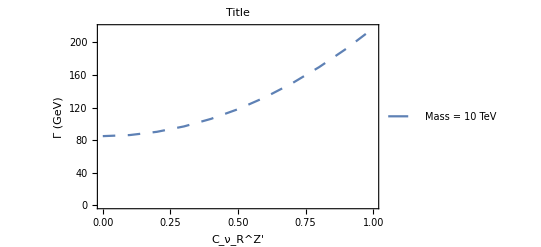

```mathematica
PlotZprimeDecayFixed1008=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

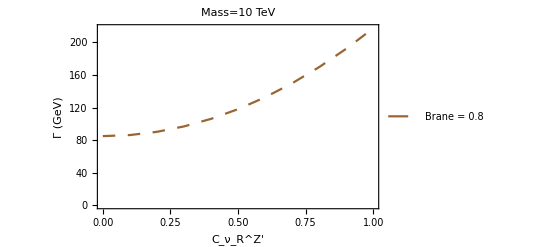

```mathematica
PlotZprimeDecayFixed1008B=ListPlot[%%, Joined-> True,PlotStyle->{Brown,Dashing[Medium]},PlotLegends->{"Brane = 0.8"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime10decayfixedmass08Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 84.8298
0.1 | 86.1536
0.2 | 90.1291
0.3 | 96.7565
0.4 | 106.036
0.5 | 117.967
0.6 | 132.549
0.7 | 149.784
0.8 | 169.67
0.9 | 192.208
1. | 217.398

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 0.8, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL08=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.8)
```

0.799871

```mathematica
Zprime8decayfixedmass08[CvR_]:=MassZprime8/(12π)(1/4(CvL08+CvR)^2+1/4(CvL08-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL08+CvR)^2-1/2(CvL08+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime8decayfixedmass08Table=Table[{Q[i],Zprime8decayfixedmass08[Q[i]]},{i,0,Npt}]
```

{{0.,67.8524},{0.1,68.9103},{0.2,72.0892},{0.3,77.3893},{0.4,84.8104},{0.5,94.3525},{0.6,106.016},{0.7,119.8},{0.8,135.705},{0.9,153.732},{1.,173.879}}

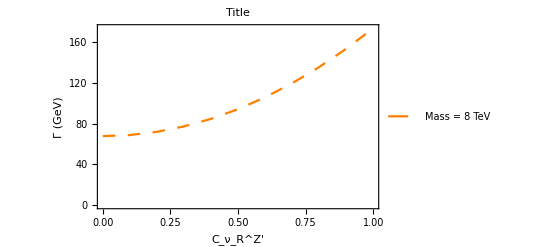

```mathematica
PlotZprimeDecayFixed808=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

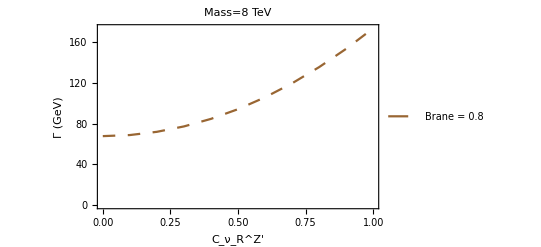

```mathematica
PlotZprimeDecayFixed808B=ListPlot[%%, Joined-> True,PlotStyle->{Brown,Dashing[Medium]},PlotLegends->{"Brane = 0.8"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime8decayfixedmass08Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 67.8524
0.1 | 68.9103
0.2 | 72.0892
0.3 | 77.3893
0.4 | 84.8104
0.5 | 94.3525
0.6 | 106.016
0.7 | 119.8
0.8 | 135.705
0.9 | 153.732
1. | 173.879

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 0.8, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL08=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.8)
```

0.799871

```mathematica
Zprime5decayfixedmass08[CvR_]:=MassZprime5/(12π)(1/4(CvL08+CvR)^2+1/4(CvL08-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL08+CvR)^2-1/2(CvL08+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime5decayfixedmass08Table=Table[{Q[i],Zprime5decayfixedmass08[Q[i]]},{i,0,Npt}]
```

{{0.,42.3767},{0.1,43.0348},{0.2,45.0176},{0.3,48.3252},{0.4,52.9574},{0.5,58.9143},{0.6,66.1959},{0.7,74.8022},{0.8,84.7332},{0.9,95.9889},{1.,108.569}}

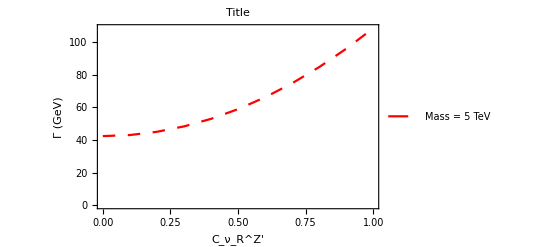

```mathematica
PlotZprimeDecayFixed508=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

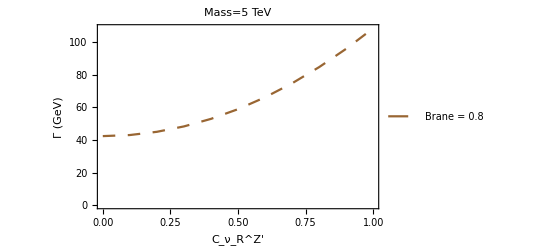

```mathematica
PlotZprimeDecayFixed508B=ListPlot[%%, Joined-> True,PlotStyle->{Brown,Dashing[Medium]},PlotLegends->{"Brane = 0.8"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime5decayfixedmass08Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 42.3767
0.1 | 43.0348
0.2 | 45.0176
0.3 | 48.3252
0.4 | 52.9574
0.5 | 58.9143
0.6 | 66.1959
0.7 | 74.8022
0.8 | 84.7332
0.9 | 95.9889
1. | 108.569

## OverLay

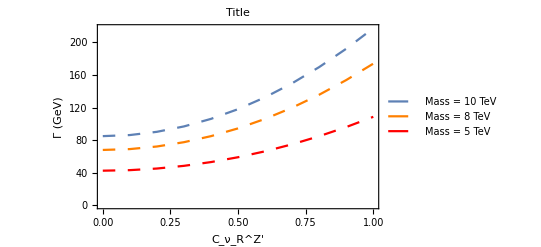

```mathematica
Show[PlotZprimeDecayFixed1008,PlotZprimeDecayFixed808,PlotZprimeDecayFixed508]
```

## OverLay 2

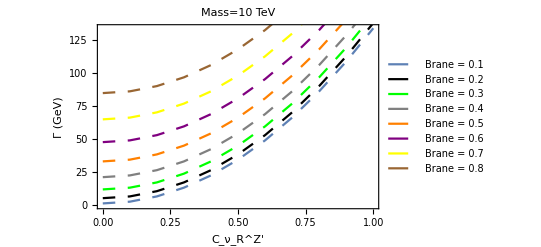

```mathematica
Show[PlotZprimeDecayFixed1001B,PlotZprimeDecayFixed1002B,PlotZprimeDecayFixed1003B,PlotZprimeDecayFixed1004B,PlotZprimeDecayFixed1005B,PlotZprimeDecayFixed1006B,PlotZprimeDecayFixed1007B,PlotZprimeDecayFixed1008B]
```

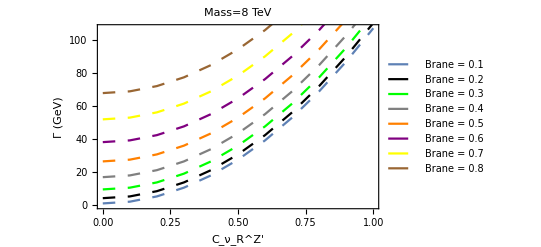

```mathematica
Show[PlotZprimeDecayFixed801B,PlotZprimeDecayFixed802B,PlotZprimeDecayFixed803B,PlotZprimeDecayFixed804B,PlotZprimeDecayFixed805B,PlotZprimeDecayFixed806B,PlotZprimeDecayFixed807B,PlotZprimeDecayFixed808B]
```

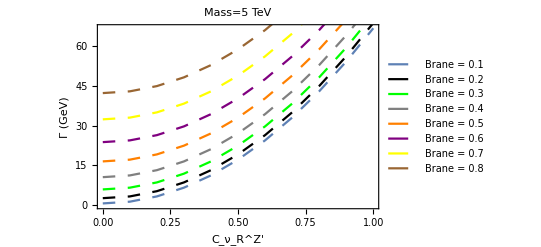

```mathematica
Show[PlotZprimeDecayFixed501B,PlotZprimeDecayFixed502B,PlotZprimeDecayFixed503B,PlotZprimeDecayFixed504B,PlotZprimeDecayFixed505B,PlotZprimeDecayFixed506B,PlotZprimeDecayFixed507B,PlotZprimeDecayFixed508B]
```